# Beam splitters and interferometry

This section develops the quantum-optical description of beam splitters and interferometers: it starts by writing the device as a lossless two-port unitary that transforms input mode operators into output modes while preserving bosonic commutators. The formalism reveals hallmark interference phenomena such as the Hong–Ou–Mandel effect, where indistinguishable photon pairs bunch into the same output port, and extends naturally to multi-element arrangements like the Mach–Zehnder interferometer, whose relative-phase control converts path-length differences into measurable intensity fringes or probabilities. An important observation is to notice quantum states have uncertainties even if we use the “most classical” states of light. A brief discussion of polarization is also included.

### Key concepts

Quantum description of beam-splitters

Mode transformation (Heisenberg evolution) and unitary evolution

Mach Zehnder Interferometer (MZI)

Wave- particle duality using single photons

Standard quantum limit

## Quantum Mechanical Description of Beam Splitters

Classically, a lossless beam splitter (BS) can be described as a device with one input mode and two output modes, related to transmitted and reflected amplitudes. However, this description is not adequate in a fully quantum approach because the commutation relations do not hold:

.

A quantum description uses an extra mode that is unused in the classical setup, but in the quantum approach it can have a quantized field in the vacuum state that has relevant physical effects. Using this description, the commutation relations hold, and we can analyze behaviors that cannot be explained classically.

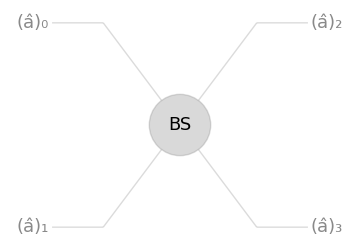
```mathematica
-Graphics--Graphics-
```

The beam splitter can be described as a device with two input modes and two output modes. The field creation operators can be related between input and output modes using the complex reflectance and transmittance coefficients

## Types of Beam Splitters

A general expression for a beam-splitter matrix that relates input and output modes:

```mathematica
GeneralBS = QuantumOperator[ⅇ^(ⅈ ϕg)({{Sin[θ] ⅇ^(ⅈ ϕr), Cos[θ] ⅇ^(-ⅈ ϕt)}, {Cos[θ] ⅇ^(ⅈ ϕt), -Sin[θ] ⅇ^(-ⅈ ϕr)}}),"Parameters"->{θ,ϕg,ϕr,ϕt}];
```

But in practice, two kinds of beam splitters are used.

Dielectric BS ; in the 50:50 case we get:

```mathematica
GeneralBS[π/4,0,0,0]["Matrix"]//Normal//TraditionalForm
```

(1/(√2) | 1/(√2)
1/(√2) | -1/(√2))

Symmetric BS ; in the 50:50 case we get:

```mathematica
GeneralBS[π/4,π/2,-π/2,0]["Matrix"]//Normal//TraditionalForm
```

(1/(√2) | ⅈ/(√2)
ⅈ/(√2) | 1/(√2))

In terms of r and t :

```mathematica
bs1 = GeneralBS[ArcSin[r],0,0,0];
```

Associated matrix t = √(1-r^2):

```mathematica
(bs1["Matrix"]//Normal)/. √(1-r^2)->t//TraditionalForm
```

(r | t
t | -r)

The evolution matrix of the beam splitter is unitary:

```mathematica
FullSimplify[SuperDagger[bs1]@bs1,0<r<1]
```

00+11

## Digression: Polarization of a Photon

The polarization degrees of freedom of a photon can be described in a quantum two-level system, which follows the same mathematical structure as the classical description with Jones vectors.

Define a basis:

```mathematica
polBasis = QuantumBasis[{"H","V"}];
```

An alternative basis is working in the diagonal and antidiagonal basis:

```mathematica
diagPolBasis =QuantumBasis@AssociationThread[{"D","A"}->QuantumBasis["X"]["Elements"]];
```

Change of basis in the Wolfram Quantum Framework:

```mathematica
QuantumState["+",polBasis]
```

1/(√2)H+1/(√2)V

```mathematica
QuantumState[%,diagPolBasis]
```

D

#### Quick exercise

Project the first photon of the |ψ^-⟩ state in diagonal polarization and plot the amplitudes in a two-photon diagonal-antidiagonal basis.

Create state:

```mathematica
psiminus = QuantumState["PsiMinus",polBasis]
```

1/(√2)HV-1/(√2)VH

Project the first photon (this means using a polarizer or projector |D⟩ ⟨D|):

```mathematica
projectionD =QuantumState["0",diagPolBasis]["Projector"]@QuantumState["PsiMinus",polBasis]
```

-1/2DH+1/2 DV

Use "AmplitudesPlot", only |DA⟩ nonzero amplitude:

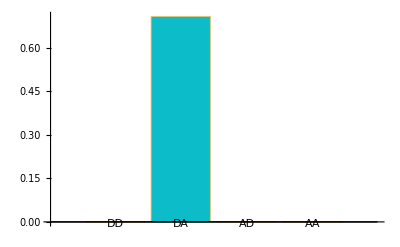

```mathematica
QuantumState[projectionD,QuantumBasis[{diagPolBasis,diagPolBasis}]]["AmplitudesPlot",ChartLegends->Automatic]
```

#### Wave plates

To change the polarization, we can use wave plates made of birefringent materials.

Half- and quarter-wave plate (HWP and QWP) definitions in the H and V polarization basis:

```mathematica
TraditionalForm[mat1=RotationMatrix[θ].{{1,0},{0,ⅇ^(ⅈ π)}}.RotationMatrix[-θ]//Simplify]
```

(cos(2 θ) | sin(2 θ)
sin(2 θ) | -cos(2 θ))

```mathematica
TraditionalForm[mat2 =RotationMatrix[θ].{{1,0},{0,ⅇ^(ⅈ π/2)}}.RotationMatrix[-θ]//Simplify]
```

(cos^2(θ)+ⅈ sin^2(θ) | (1-ⅈ) sin(θ) cos(θ)
(1-ⅈ) sin(θ) cos(θ) | sin^2(θ)+ⅈ cos^2(θ))

Wrapping matrices in QuantumOperators:

```mathematica
HWP = QuantumOperator[mat1,polBasis,"Parameters"->θ];
```

```mathematica
QWP = QuantumOperator[mat2,polBasis,"Parameters"->θ];
```

Single-qubit gates:

```mathematica
HWP[π/4]==QuantumOperator["X"]
```

True

```mathematica
HWP[π/8]==QuantumOperator["H"]
```

True

```mathematica
HWP[π/4][]
```

V

In general, any operator that belongs to SU(2) in polarization space can be realized with a sequence of QWP-HWP-QWP operations.
“Minimal three-component SU(2) gadget for polarization optics” – R. Simon and N. Mukunda (1990)

## Evolution of Quantum States in Beam Splitters

Define the output modes:

```mathematica
a2=a;
a3=QuantumOperator[a,{2}];
```

We use a symmetric 50:50 beam splitter:

```mathematica
balancedBS =GeneralBS[π/4,π/2,-π/2,0];
```

We calculate the inverse because in this case, we find input modes in terms of output modes (Heisenberg-like evolution):

```mathematica
{a0,a1} = Inverse@balancedBS["Matrix"].{a2,a3};
```

Evolution of a one-photon state :

```mathematica
onePhotonEvolve = a1["Dagger"][]
```

1/(√2)01+ⅈ/(√2)10

The output state results in a entangled state see QuantumEntanglementMonotone (default metric is “Concurrence”):

```mathematica
QuantumEntanglementMonotone[onePhotonEvolve,{1,2}]
```

1

If we put one photon in each of the input ports, the two photons emerge together. That is explained by interference when the photons are indistinguishable (Hong–Ou–Mandel effect).

:

```mathematica
twoPhotonEvolve = SuperDagger[a0]@SuperDagger[a1][]
```

QuantumState[…]

There is also possible to adopt a Schrodinger picture approach and for the 50:50 symmetric beam splitter we have the unitary

```mathematica
a0=a;
a1=QuantumOperator[a,{2}];
```

Defining the unitary:

```mathematica
U = QuantumOperator[MatrixExp[ⅈ π/4.(SuperDagger[a0]@a1+a0@SuperDagger[a1])],"Label"->"U"];
```

Representing the evolution as a circuit:

```mathematica
photonEvolve = QuantumCircuitOperator[{FockState[{1,1}],U}];
```

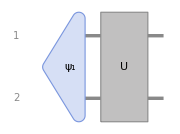

```mathematica
photonEvolve["Diagram",ImageSize->Small]
```

Schrodinger picture evolution:

```mathematica
Chop[photonEvolve[]]
```

(0.+0.707107 ⅈ)02+(0.+0.707107 ⅈ)20

## Evolution of Quantum States in Beam Splitters (II)

Now let’s try using a coherent state in the input port one  , using :

Numerical amplitude:

```mathematica
αcoh = RandomReal[{0,1.5}]Exp[I RandomReal[{0,2Pi}]];
```

Input modes in terms of output modes:

```mathematica
{a0,a1} = Inverse@balancedBS["Matrix"].{a2,a3};
```

Calculating the output state:

```mathematica
cohBS = MatrixExp[(αcoh a1["Dagger"]-αcoh* a1)][]//Chop;
```

The entanglement monotone is really close to zero, so it is a product state (not entangled):

```mathematica
QuantumEntanglementMonotone[cohBS,{{1},{2}}]
```

3.65002×10^-8

The theoretical result represents that a coherent state resembles a classical field that divides evenly in a 50:50 BS (average photon number |α|^2/2 in each output mode and phase shift π/2 for the reflected wave):

Comparing the states:

```mathematica
(cohBS -(coherent[ⅈ αcoh/√2] //coherent[αcoh/√2]))//Chop
```

0

Also, the beam splitter causes the transformation that N photons are binomially distributed over the two modes.

Let’s verify that for a particular N, :

```mathematica
Np = 8;
```

```mathematica
outstate = (Nest[a1["Dagger"],FockState[{0,0}],Np]//Simplify)/√(Np!);
```

Output state:

```mathematica
outstate//TraditionalForm
```

1/16 08+ⅈ/(4 √2)17-(√7)/826-1/4 ⅈ √(7/2)35+(√(35/2))/8 44+1/4 ⅈ √(7/2)53-(√7)/862-ⅈ/(4 √2)71+1/16 80

```mathematica
probs =outstate["Probability"]//Values;
```

Plot of the photon distribution over the two modes:

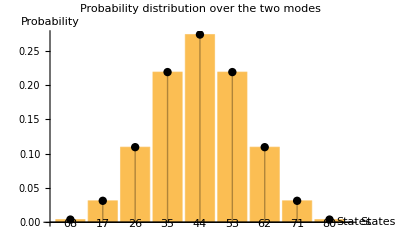

```mathematica
Show[outstate["ProbabilityPlot",AxesLabel->{"States","Probability"}],ListPlot[Table[{k+1,PDF[BinomialDistribution[Np,0.5],k]},{k,0,Np}],PlotStyle->{Black,PointSize[0.015]},Filling->Axis],PlotLabel->"Probability distribution over the two modes"]
```

## Single-Photon Mach–Zehnder Interferometer

```mathematica
SetFockSpaceSize[3];
```

```mathematica
a5 = a;
a6 =QuantumOperator[a,{2}];
```

We now use a dielectric beam splitter:

```mathematica
balancedBS = GeneralBS[π/4,0,0,0];
```

Compute the operator of the arrangement:

```mathematica
MZ = balancedBS@QuantumOperator["P"[ϕ]]@balancedBS;
```

Relating the final and initial operators (Heisenberg-like evolution):

```mathematica
{a1,a2} = Inverse@MZ["Matrix"].{a5,a6};
```

```mathematica
probs = (a1["Dagger"]@QuantumState["00",{$FockSize,$FockSize}])["Probability"]
```

<|01→(ⅇ^(2 Im[ϕ]) Abs[-1/2+1/2 ⅇ^(-ⅈ Conjugate[ϕ])]^2)/(ⅇ^(2 Im[ϕ]) Abs[-1/2+1/2 ⅇ^(-ⅈ Conjugate[ϕ])]^2+ⅇ^(2 Im[ϕ]) Abs[1/2+1/2 ⅇ^(-ⅈ Conjugate[ϕ])]^2),10→(ⅇ^(2 Im[ϕ]) Abs[1/2+1/2 ⅇ^(-ⅈ Conjugate[ϕ])]^2)/(ⅇ^(2 Im[ϕ]) Abs[-1/2+1/2 ⅇ^(-ⅈ Conjugate[ϕ])]^2+ⅇ^(2 Im[ϕ]) Abs[1/2+1/2 ⅇ^(-ⅈ Conjugate[ϕ])]^2)|>

```mathematica
simplifiedProbs = FullSimplify[probs//Values,Element[ϕ,Reals]]//ComplexExpand //TrigReduce
```

{1/2 (1-Cos[ϕ]),1/2 (1+Cos[ϕ])}

```mathematica
Plot[Evaluate@MapThread[Callout[#1,#2,Right]&,{simplifiedProbs,{"D1","D2"}}],{ϕ,0,6Pi},
AxesLabel->{"ϕ","Probability"},
PlotLegends->{"Output 5","Output 6"}]
```

-Graphics-

## Interference of coherent states

Let’s analyze the interferometry of coherent states in a Mach–Zehnder interferometer. We should expect similar results as using classical light, calling ĉ and d̂ the final output modes after the second BS.

Let’s follow a similar procedure as the previous case:

```mathematica
SetFockSpaceSize[30];
RandomSeed[150];
αcoh = 1.8Exp[I RandomReal[{0,2Pi}]];
```

Balanced symmetric BS:

```mathematica
balancedBS =GeneralBS[π/4,π/2,-π/2,0];
```

Modes operators:

```mathematica
c= a;
d =QuantumOperator[a,{2}];
```

Operator of the arrangement:

```mathematica
MZ = QuantumOperator[balancedBS@ QuantumOperator["P"[ϕ]]@balancedBS,"Parameters"->ϕ];
```

We can calculate the evolution for some particular θ:

```mathematica
θx = RandomReal[{0,2π}];
{a0,a1} = Inverse@MZ[θx]["Matrix"].{c,d};
```

```mathematica
outstate =Exp[(αcoh SuperDagger[a1]-αcoh* a1)][];
```

As expected, it should be a product state:

```mathematica
QuantumEntanglementMonotone[outstate,{{1},{2}}]
```

2.41656×10^-7

It can be shown that the analytical expression for the evolution is:

.

Verifying the result numerically:

```mathematica
Chop[outstate -(coherent[(ⅈ(1+ⅇ^(ⅈ θx))αcoh)/2]//coherent[(( ⅇ^(ⅈ θx)-1)αcoh)/2])]
```

0

Phase shift θ can be measured by subtracting the intensities from two detectors, D_1 and D_2. That can be represented by ⟨Ô ⟩ with Ô=c^†c-d^†d  the number difference operator. This is simple to calculate, because the mean of the number operator on a coherent state is just the magnitude of the complex squared:

```mathematica
Ocurrent = SuperDagger[c]@c -SuperDagger[d]@d;
```

The mean of the Ô operator can be calculated symbolically:

```mathematica
OmeanSymbolic = FullSimplify[Abs[(ⅈ (ⅇ^(ⅈ θ)+1)α)/2]^2-Abs[((ⅇ^(ⅈ θ)-1)α)/2]^2,Element[θ,Reals]]
```

α Conjugate[α] Cos[θ]

It has to agree with the value computed using our quantum state:

```mathematica
Chop[(SuperDagger[outstate]@Ocurrent@outstate)["Scalar"]]/Norm[αcoh]^2
```

0.493692

```mathematica
Cos[θx]
```

0.493692

We observe the result analogous to classical coherent light, but coherent states are still quantum states and possess quantum mechanical fluctuations. Using error propagation, the uncertainty of phase measurement is

,

which is optimal or minimum for odd multiples of π/2. That is the best result with classical-like states determining a standard quantum limit.

It is possible to beat that limit using non-classical light; for example, that is discussed in large-scale interferometers to detect gravitational waves (LIGO).

## Paclet installation

Install  the Quantum Framework paclet:

```mathematica
PacletInstall["https://www.wolfr.am/DevWQCF",ForceVersionInstall->True]
```

PacletObject[…]

Load quantum framework functions:

```mathematica
Needs["Wolfram`QuantumFramework`"]
```

Load quantum framework functions for the second quantization:

```mathematica
Needs["Wolfram`QuantumFramework`SecondQuantization`"]
```

Useful definitions:

```mathematica
a := AnnihilationOperator[]
coherent := CoherentState[]["Normalize"]
```